{{a[n]→1/2 (3 Fibonacci[n]+LucasL[n])}}

Some results

3, 13, 55, 144

The Solution for the DiscretePlot

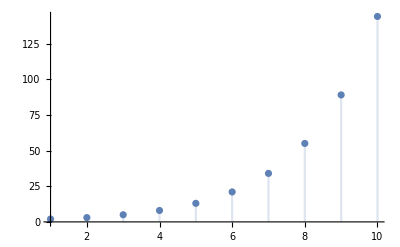

```mathematica
Clear["`*"];
(*Initial Values*)
iv1=a[1]==2;
iv2=a[2]==3;
(*Our Recurrent relation is defined below*)
rr=a[n]==a[n-1]+a[n-2];

sol=RSolve[{rr,iv1,iv2},a[n],n]//Simplify

a[n_]=a[n]/.sol[[1]];
"Some results"
Print[a[2],", ",a[5],", ",a[8],", ",a[10]]
"The Solution for the DiscretePlot"


DiscretePlot[a[n],{n,10}]
```